```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];

(*record/experimental parameters to be set*)
FACTOR=(1/3.1603)*1*^-6;(*µm per px*)
FPS=1.;(*frame rate in frames per second*)
DP=9.363*^-6;(*inner diameter of the pipette in m*)
DV=52.26*^-6;(*diameter of the aspirated GUV at t=0 (pre-perfusion) in m*)
CIN=400.; (*GUV internal osmolarity at t=0, mol/m.b3, mM*)
COUT=456.; (*perfusion osmolarity, mol/m.b3, mM*)

(*physical constants*)
VW=18.*^-6;(*molecular volume of water in mol/m.b3*)

(*other declarations*)
STYLE={Frame->True,PlotRange->All,ImageSize->Medium,LabelStyle->Directive[10,Black]};

(*read-in*)
FILE="Line pixle.csv";
profiles=Import[FILE];
profiles=profiles[[2;;,2;;]];
profiles=GaussianFilter[#,3]&/@profiles;

(*estimate initial position of the protrusion*)
initialPosition=First[PositionSmallest[profiles[[1]]]];

Show[
ListLinePlot[profiles,
FrameLabel->{"position (px)","intensity (au)"},PlotStyle->Directive[Gray,Opacity[0.5]],STYLE],
ListLinePlot[profiles[[1]],
PlotStyle->Red,STYLE],
GridLines->{{{initialPosition,Directive[Blue,Thick,Opacity[1]]}},None},Method->{"GridLinesInFront"->True}];
Rasterize[%,ImageResolution->600,ImageSize->Medium]
```

-Graphics-

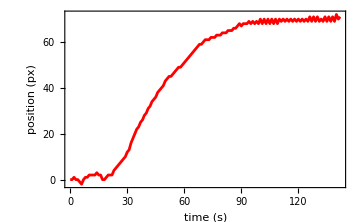

```mathematica
(*analysis parameters to be set*)
DROPLEFT=5;(*pixels to the left of each position to be disregarded*)
DROPRIGHT=20;(*pixels to the right of each position to be disregarded*)

(*analyze line profiles: find minima*)
POS={initialPosition};
Map[
Function[profile,
dropLeft=POS[[-1]]-DROPLEFT;
dropRight=Length@profile-POS[[-1]]-DROPRIGHT;
dropProfile=Drop[profile,dropLeft];
dropProfile=Drop[dropProfile,-dropRight];
smallestPositions=PositionSmallest[dropProfile,3];
nearest=First[Nearest[Flatten[smallestPositions],POS[[-1]]]];
AppendTo[POS,nearest+dropLeft];
],profiles[[1;;]]];
DROPLEFT=0;DROPRIGHT=0;

POS=(POS-POS[[1]]);
time=Range[0.,Length@POS-1]/FPS;

ListLinePlot[{time,POS}ᵀ,
FrameLabel->{"time (s)","position (px)"},PlotStyle->Red,STYLE]
```

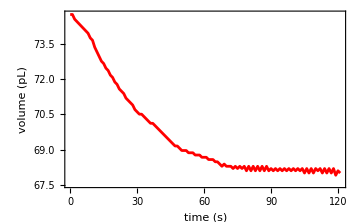

```mathematica
(*analysis parameters to be set*)
T0=21;(*time (in s) at the onset of perfusion/volume change*)

(*volume calculation acc. Appendix in Olbrich, Rawicz, Needham, Evans,Water permeability and mechanical strength of polyunsaturated lipid bilayers. Biophys J. 79, 321–327 (2000).*)
ClearAll[Lp,Acap,Acyl,Vcap,Vcyl,u,Aves,Vves,A,A0,𝒟v,V];

(*hemispherical cap and cylindrical portion of the projection inside the pipette*)
Acap=Pi*DP^2/2;
Acyl=Pi*DP*(Lp-DP/2);
Vcap=Pi*DP^3/12;
Vcyl=Pi*DP^2*(Lp-DP/2)/4;

(*spherical segment of the vesicle region outside the pipette*)
u=Sqrt[(1-(DP/𝒟v)^2)];
Aves=Pi*𝒟v^2*(1+u)/2;
Vves=Pi*𝒟v^3*(2+3u-u^3)/24;

(*total area and area geometric constraint*)
A=Acap+Acyl+Aves;
A0=(Acap+Aves)/.(𝒟v->DV);(*ASSUMPTION: since Lp=DP/2 is assumed at t=0, the initial cylindrical area is exactly 0*)

(*expression for 𝒟v (vesicle diameter as a function of protreusion length assuming constant area constraint); it is obtained as the second output (root) of Solve[A0==A,𝒟v]//FullSimplify (note that this can be run only after the declaration of the necessary variables (that is, further below))*)
𝒟v=(√(DP^5-8 DP^4 Lp-8 (1+√(1-DP^2/DV^2)) DV^4 Lp-4 DP^2 Lp ((6+√(1-DP^2/DV^2)) DV^2+4 Lp^2)+DP^3 (7 DV^2+20 Lp^2)+4 DP DV^2 ((1+√(1-DP^2/DV^2)) DV^2+2 (3+√(1-DP^2/DV^2)) Lp^2)))/(√(DP^3-8 DP^2 Lp-16 DV^2 Lp+8 DP (DV^2+2 Lp^2)));

(*total volume*)
V=Vcap+Vcyl+Vves;

(*subsituting the list of protrusion lengths*)
Lp=POS*FACTOR;(*list of projection lengths from edge tracking in µm; note that Lp(time=0)=0, not the actual protrusion length due to, e.g., osmolarity mismatches and applied suction pressure (tension)*)
Lp=Lp+DP/2;(*ASSUMPTION: set the minimum physical projection length*)

(*constructing the time dependence*)
Vt={time,V*1.*^15}ᵀ;(*volume (in pL) over time*)
Vt=Select[Vt,#[[1]]>=T0&];
Vt=MapAt[#-Vt[[1,1]]&,Vt,{All,1}];

ListLinePlot[Vt,
FrameLabel->{"time (s)","volume (pL)"},PlotStyle->Red,STYLE]
```

{τ→30.1191,a→-7.67242,o→75.4408}

P_f from exponential fit with Hannesschläger correction: 33.07 µm/s

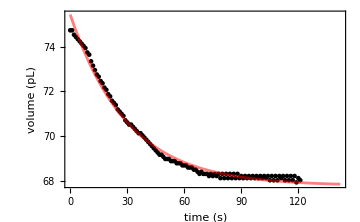
{-Graphics-,profiles | Line pixle.csv
factor (µm/px) | 0.316426
frames per second | 1.
aspirated GUV diameter (µm) | 52.26
pipette diameter (µm) | 9.363 .08
cin at t=0 (mM) | 400.
cout (mM) | 456.
P_f acc. Hannesschläger (µm/s} | 33.07}

```mathematica
(*exponential fitting procedure*)
ClearAll[fExp,T];
(*fExp[t_,τ_,a_,b_,t0_]=Piecewise[{
{0,t<t0},
{b*(1-Exp[-(t-t0)/τ]),t>=t0}
}];*)
fExp[t_,τ_,a_,o_]:=a*(1-Exp[-t/τ])+o

expFit=NonlinearModelFit[Vt,(*Table[{t,Interpolation[Vt,InterpolationOrder->1][t]},{t,time[[1]],time[[-1]],0.01}]*)
fExp[t,τ,a,o],
{{τ,10.},{a,10.},{o,Vt[[1,2]]}},
t,
MaxIterations->1000,PrecisionGoal->Infinity];(* fitting the simulated trace with the exponential model *)
expParams=expFit["BestFitParameters"]
T=τ/.expParams;

PfHannesschlaeger[iT_,cout_,cin_,r0_]:=r0/(3*VW*iT)*(cin+cout)/(2*cout^2);
"P_f from exponential fit with Hannesschläger correction: "<>ToString[NumberForm[PfHannesschlaeger[T,COUT,CIN,DV/2]*1.*^6,{10,2}]]<>" µm/s"

{Show[
ListPlot[Vt,
FrameLabel->{"time (s)","volume (pL)"},PlotStyle->Black,STYLE],
Plot[expFit["Function"][t],{t,time[[1]],time[[-1]]},
PlotStyle->Directive[Red,Opacity[0.5]]],STYLE],
Grid[{{"profiles",FILE},
{"factor (µm/px)",FACTOR*1*^6},
{"frames per second",FPS},
{"aspirated GUV diameter (µm)",DV*1*^6},
{"pipette diameter (µm)",DP.08*1*^6},
{"cin at t=0 (mM)",CIN},
{"cout (mM)",COUT},
{"P_f acc. Hannesschläger (µm/s}",NumberForm[PfHannesschlaeger[T,COUT,CIN,DV/2]*1.*^6,{10,2}]}},
Frame->All]}
```

{Pf→0.000043098,cout→449.078}

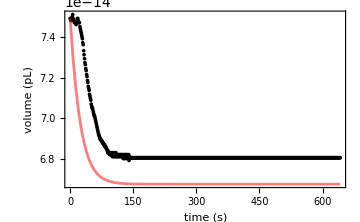

P_f from Lambert fit: 43.10 µm/s

```mathematica
(*Analytical (Lambert) fitting procedure*)
(*derived parameters*)
Vt={time,V}ᵀ;
Vt=Join[Vt,{#*(Differences[time][[1]])+time[[-1]],Mean[V[[-5;;-1]]]}&/@Range[500]];(*some padding at the end to the the Lambert fit to converge*)
V0=Vt[[1,2]];
A0=4*Pi*(DV/2)^2;

(*Lambert/analytical fit*)
ClearAll[LambertV];
LambertV[t_,cin_,cout_,v0_,a0_,Pf_]:=(cin v0 (1+ProductLog[((-cin+cout) ⅇ^(-1+(cout (v0-a0 cout Pf t VW))/(cin v0)))/cin]))/cout;

LambertFit=NonlinearModelFit[Vt,
LambertV[t,CIN,cout,V0,A0,Pf],
{{Pf,50.*^-6},{cout,450}},
t,
PrecisionGoal->Infinity];
LambertParams=LambertFit["BestFitParameters"]

Show[
ListPlot[Vt,
FrameLabel->{"time (s)","volume (pL)"},PlotStyle->Black,STYLE],
Plot[LambertFit["Function"][t],{t,Vt[[1,1]],Vt[[-1,1]]},
PlotStyle->Directive[Red,Opacity[0.5]],PlotRange->All],
STYLE]

"P_f from Lambert fit: "<>ToString[NumberForm[(Pf/.LambertParams)*1.*^6,{10,2}]]<>" µm/s"
```

## Lambert derivation

```mathematica
Clear[A,V0,V,VW];
eqD=D[V[t],t]==Pf*A*VW*(cin*V0/V[t]-cout)
DSolve[{eqD,V[0]==V0},V[t],t]//FullSimplify//Quiet;
V[t]/.First[%]
```

V'[t]==A Pf VW (-cout+(cin V0)/V[t])

(cin V0 (1+ProductLog[((-cin+cout) ⅇ^(-1+(cout (V0-A cout Pf t VW))/(cin V0)))/cin]))/cout